Last modified on: Tuesday, July 10, 2018 at 19:11

Author Info

Ian Fan

Sebastian Bodenstein

University of Melbourne

Poster Session Content

Reinforcement Q-Learning for Atari Games

This project aims to create a neural network agent that plays Atari games. This agent is trained using Q-Learning. The agent will not have any priori knowledge of the game and able to learn by playing the game and only being told when it loses.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics--Graphics-

Successfully implement classical q-learning agent on CartPole environment, able to achieve average performance of 195 episodes in 300 games. Tried to add time information in the input, the agent achieve 8k episodes within 300 games.

Make the Q-learning agent with multiple observation as input perform more stable and implement different techniques that increase the network’s performance like DDQN, Noisy net, etc.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

What is Reinforcement Learning

An area of Machine Learning, inspired by behaviourist psychology
Agent learn how to behave in a environment by performing actions and seeing the results.

Agent starts with state 0,
Agent chooses action A0,
Agent receives reward R0,
Agent goes to state 1, continue

-Graphics-

Value Network and Policy Network

In value-based RL, the input will be the current state or a combination of few recent states, and the output will be the estimated future reward of every possible action at this state. The goal will be to optimize the value function.

In policy-based RL, the input will be the current state or a combination of few recent states, and the output will be the most appropriate action at this state. The goal will be to optimize the policy function.

-Graphics--Graphics-

Deep Q Network

Give a state, the Q function predicts the total reward that it will received till the game is end of each action. The amazing part is that the Q function is predicting its own output. It uses a function to predict the result of iteratively evaluate every state.

-Graphics-

DQN in  CartPole

Here are there list animate shows the result of reinforcement learning on CartPole. The first is a random agent which does random action no matter the state. It’s average performance is around 23 episodes per game. The second agent is the result of classical DQN agent which only takes current observation as input, its average performance is around 3000. The third agent is also DQN agent but takes the current observation and previous observation as input, it has a performance of 8000 and peak performance actually reaches 10,000 which is the limit I set for this game.

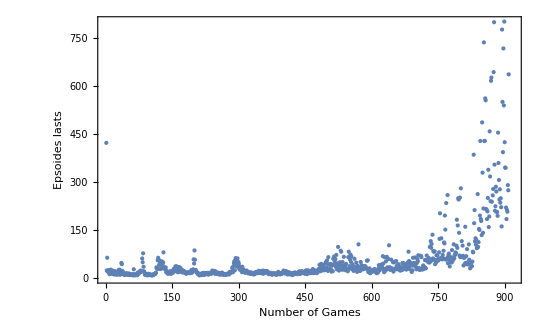
(* The sample play of Random Agent *)

(* The sample play of DQN agent 1 *)

(* The sample play of DQN agent 2 *)
-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

The main environment for agent to learn and  tested is CartPole environment. This environment is consist of two movable parts. One is the cart which is controlled by the agent, has two possible action every state which is moving left or right. The other one is pole. This environment simulate the effect of gravity on pole which makes it fall to left or right due to its orientation with the horizon.  For this environment to be considered as solved, the average episodes that the agent able to get in 100 games is over 195.  Following graph is a visual representation of the environment. The blue rectangle represents the pole. The black box is the cart. The black line is the horizon.
  -Graphics-
  In this project, I built three agents to solve this environment.
1. The first one is a policy gradient agent that able to solve the CartPole environment within 2000 game plays.
The Net Layer of this agent is using 2 linear layers with size 16 and using Ramp as activation function. And one layer of size 2 with softmax as the output. This agents uses Discounted Reward to calculate the reward for each action. Discounted Reward is a back tracking algorithm for assigning the reward for every action be done in one game. The reward of certain action T is the sum of the reward from state T to ending state with a discount factor gamma. In this game, using Discounted Reward able to make the actions keep the agent alive being rewarded more than actions that leads to the pole falling down.
. 
2. The second agent is a classical Deep Q learning agent which takes a representation of the current observation of the state and outputs the estimated future reward of all possible actions. The Net Structure of this agent is two linear layers with size 64 and Tanh as activation function and an output layer with size 2. I am using Tanh here as activation function since here DQN is a value network instead policy network which means it is doing regression instead of classification. The basic idea of DQN is that all future state is related to the current state so that there exists a Q function takes in a state and able to output the sum of the future rewards.
-Graphics-
The result of this approach is that able to solve the CarPole environment with in 300 games.
3. The third agent is also a DQN agent but instead taking current observation as input, the agent takes a combination of current state and previous state as input. This approach gives the agent time information of the game. In the CartPole environment, the combination of 2 states gives information of the direction that the pole is falling to.

#### Code

Provide one of:

https://github.com/ianfanx/wss2018Project

#### Written Content / Lesson Plans

#### Conclusions in Detail

The conclusion are following:
1. the DQN agent is hard to converge, but once it converge, the performance is outstanding.
2. Extra observation gives agent more information of the game which usually results in better choice of action.
3. Compare to policy network, value network is harder to understand.

#### All Visualizations

#### Data Sources Links/References

https://medium.freecodecamp.org/an-introduction-to-reinforcement-learning-4339519de419

#### Future Directions

Increase the stability of the current method (take in multiple observation as input)
Let the agent play on Pong
Combine value network with different technique including DDQN, A3C, Noisy Net, etc and implement Rainbow algorithm

#### Background Info Links/References

https://www.cs.toronto.edu/~vmnih/docs/dqn.pdf
https://gym.openai.com/
https://arxiv.org/pdf/1710.02298.pdf
https://medium.freecodecamp.org/diving-deeper-into-reinforcement-learning-with-q-learning-c18d0db58efe

#### Keywords

Provide keywords as items

Reinforcement Learning

Deep Q Network

#### Other information